```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["data.xlsx"][[1]][[2;;9,4;;6]];
```

```mathematica
plotData=Transpose[{
Join[
data[[All,1]],
Reverse[data[[All,1]]]
],
Join[
data[[All,2]],
Reverse[data[[All,3]]]
]
}]
```

{{49.,69.3},{45.,63.8},{40.,64.9},{35.,58.3},{30.,63.8},{25.,66.},{20.,66.},{15.,66.},{15.,77.},{20.,82.5},{25.,89.1},{30.,86.9},{35.,90.2},{40.,101.2},{45.,104.5},{49.,105.6}}

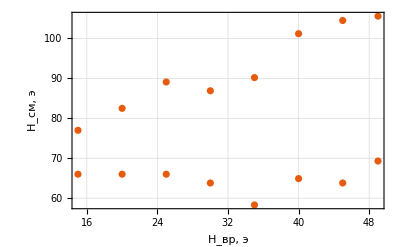

```mathematica
plot=ListPlot[plotData,PlotTheme->"Scientific",GridLines->Automatic,FrameLabel->{"H_(:0432:0440), э", "H_(:0441:043c), э"}]
```

```mathematica
Export["plot.pdf",plot]
```

plot.pdf

```mathematica
(*Подгоняем под эллипс*)
```

```mathematica
lin={#1^2,#1,#2,2#1#2,#2^2}&@@@plotData;
```

```mathematica
lm=LinearModelFit[lin,{1,a,b,c,d},{a,b,c,d}]
```

FittedModel[-4052.35-0.318136 a-45.3094 b+124.066 c+0.492439 d]

```mathematica
lm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -4052.35 | 542.265 | -7.47301 | 0.0000124107
a | -0.318136 | 0.237607 | -1.33892 | 0.20761
b | -45.3094 | 17.3549 | -2.61075 | 0.0242249
c | 124.066 | 7.49768 | 16.5473 | 4.03827×10^-9
d | 0.492439 | 0.0940312 | 5.23697 | 0.000278118

```mathematica
pa=lm["BestFitParameters"];
```

```mathematica
w[x_,y_]:=pa.{1,x^2,x,y,2 x y}-y^2;
```

```mathematica
pol={x/.Solve[D[y/.NSolve[-w[x,y]==0,y][[1,1]],x]==0,x][[1]],y/.Solve[D[x/.NSolve[-w[x,y]==0,x][[1,1]],y]==0,y][[1]]}
```

{25.3454,68.8579}

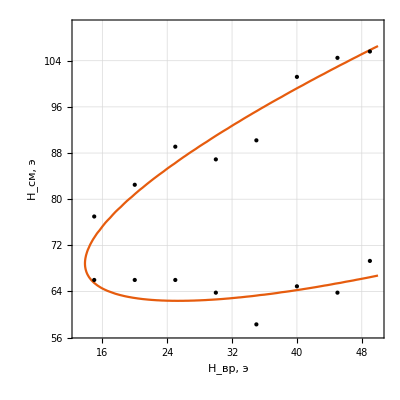

```mathematica
plot2=ContourPlot[w[x,y]==0,{x,13,50},{y,57,110},Epilog->Point[plotData],PlotTheme->"Scientific",GridLines->Automatic,FrameLabel->{"H_(:0432:0440), э", "H_(:0441:043c), э"}]
```

```mathematica
TeXForm[TraditionalForm[-w[x,y]==0]]
```

0.318136 x^2-0.984878 x y+45.3094 x+y^2-124.066 y+4052.35=0

```mathematica
TeXForm[lm["ParameterTable"]]
```

\begin{array}{l|llll}
 \text{} & \text{Estimate} & \text{Standard Error} & \text{t-Statistic} & \text{P-Value} \\
\hline
 1 & -4052.35 & 542.265 & -7.47301 & 0.0000124107 \\
 a & -0.318136 & 0.237607 & -1.33892 & 0.20761 \\
 b & -45.3094 & 17.3549 & -2.61075 & 0.0242249 \\
 c & 124.066 & 7.49768 & 16.5473 & \text{4.0382683680157065$\grave{ }$*${}^{\wedge}$-9} \\
 d & 0.492439 & 0.0940312 & 5.23697 & 0.000278118 \\
\end{array}

```mathematica
Export["plot2.pdf",plot2]
```

plot2.pdf

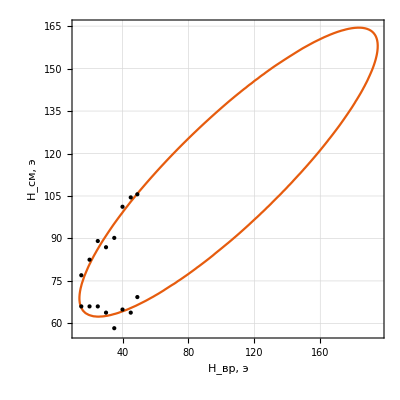

```mathematica
plot3=ContourPlot[w[x,y]==0,{x,13,195},{y,57,165},Epilog->Point[plotData],PlotTheme->"Scientific",GridLines->Automatic,FrameLabel->{"H_(:0432:0440), э", "H_(:0441:043c), э"}]
```

```mathematica
pol={
x/.Solve[D[y/.NSolve[-w[x,y]==0,y][[1,1]],x]==0,x][[1]],y/.Solve[D[x/.NSolve[-w[x,y]==0,x][[1,1]],y]==0,y][[1]],
x/.Solve[D[y/.NSolve[-w[x,y]==0,y][[2,1]],x]==0,x][[1]],
y/.Solve[D[x/.NSolve[-w[x,y]==0,x][[2,1]],y]==0,y][[1]]
}
```

{25.3454,68.8579,183.349,157.978}